# Electric Field Plots

```mathematica
dipole=1/(√(x^2+(-y-1/2)^2))-1/(√(x^2+(1/2-y)^2));
```

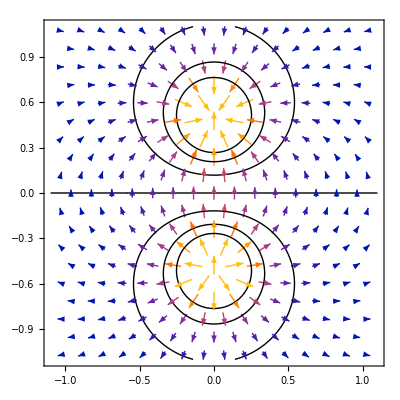

```mathematica
PotentialElectricFieldPlot[dipole,
{x,1.1,-1.1},{y,1.1,-1.1}]
```

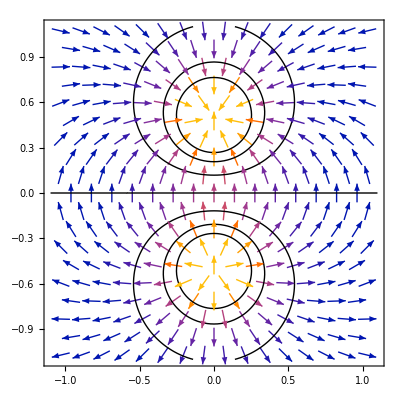

```mathematica
PotentialElectricFieldPlot[dipole,
{x,1.1,-1.1},{y,1.1,-1.1},VectorScaling->None]
```

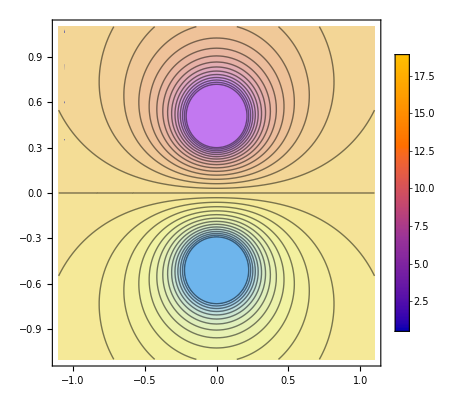

```mathematica
PotentialElectricFieldPlot[
dipole,
{x,-1.1,1.1},
{y,-1.1,1.1},
ContourShading->Automatic,
PlotRange->Automatic,
ColorFunction->"Pastel",
ClippingStyle->Automatic,
Contours->30,
PlotLegends->Automatic
]
```

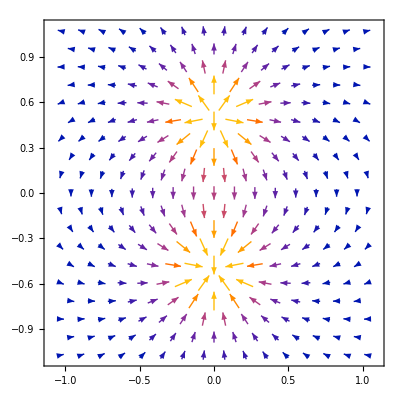

```mathematica
GradientFieldPlot[dipole,{x,-1.1,1.1},{y,-1.1,1.1}]
```

## Options

```mathematica
Options[GradientFieldPlot]==Options[VectorPlot]
```

True

```mathematica
ops=Complement[Options[ContourPlot],Options[VectorPlot]]
Length[ops]
```

{ClippingStyle→None,ColorFunction→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,Exclusions→Automatic,ExclusionsStyle→None,MeshFunctions→{},PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},ScalingFunctions→None}

13

```mathematica
FilterRules[{ClippingStyle->Automatic,ColorFunction->None,PlotPoints->Automatic},Options[VectorPlot]]
```

{ClippingStyle→Automatic,ColorFunction→None}

```mathematica
Options[VectorPlot]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→Automatic,ColorFunction→None,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→Automatic,MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotRange→{Full,Full},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionBoundaryStyle→Automatic,RegionFillingStyle→Automatic,RegionFunction→(True&),RotateLabel→True,StreamColorFunction→Automatic,StreamColorFunctionScaling→True,StreamMarkers→Automatic,StreamPoints→None,StreamScale→Automatic,StreamStyle→Automatic,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},VectorAspectRatio→Automatic,VectorColorFunction→Automatic,VectorColorFunctionScaling→True,VectorMarkers→Automatic,VectorPoints→Automatic,VectorRange→Automatic,VectorScale→None,VectorScaling→None,VectorSizes→Automatic,VectorStyle→Automatic,WorkingPrecision→MachinePrecision}

## Evaluate

```mathematica
Evaluate[D[Sin[x],x]]
```

Cos[x]

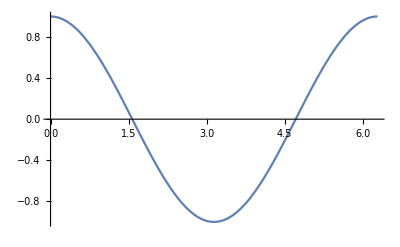

```mathematica
Plot[Cos[x],{x,0,2π}]
```

```mathematica
Plot[Evaluate[D[Sin[x],x]],{x,0,2π}]
```

-Graphics-

Propiedades de Table : Al pasar los argumentos a Table las variables de entrada estan congeladas y no se han evaluado.

```mathematica
iter={i,1,10};
```

```mathematica
Table[i,iter]
```

Table::nliter: Non-list iterator iter at position 2 does not evaluate to a real numeric value.

Table[i,iter]

No reconoce a iter como la lista de iteracion de 1 a 10. Esto debido a que iter no pasa como evaluacion, si no como una variable “iter”.

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

Se arregla este problema con Evaluate, esta funcion evalua una expresion antes que entre al algoritmo o fuerza una evaluacion incluso si no se pide que se lo haga.

```mathematica
Table[i,Evaluate@iter]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ff=i^2;
```

```mathematica
Table[ff,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Se debe revisar los atributos de la funcion para ver si tiene el atributo Hold o HoldAll.

```mathematica
Attributes[Table]
```

{HoldAll,Protected}

```mathematica
Attributes[Plot]
```

{HoldAll,Protected,ReadProtected}

```mathematica
func=Table[Sin[i x],{i,1,5}]
```

{Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x]}

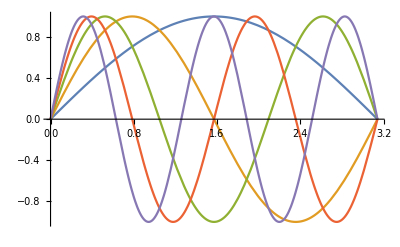

```mathematica
Plot[func,{x,0,π}](*Se pasa la tabla func despues de evaluar*)
```

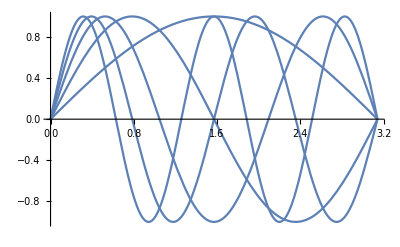

```mathematica
Plot[Table[Sin[i x],{i,1,5}],{x,0,π}](*Se pasa la tabla sin evaluar, el algoritmo interno de mathematica interpreta todo el Table[Sin...]] como una unica funcion y por ello sale todo graficado de un solo color*)
```

Para arreglarlo nuevamente se usar Evaluate.

```mathematica
Plot[Evaluate[Table[Sin[i x],{i,1,5}]],{x,0,π}]
```

-Graphics-

Evaluate tambien se puede utilizar para acelerar una iteracion:

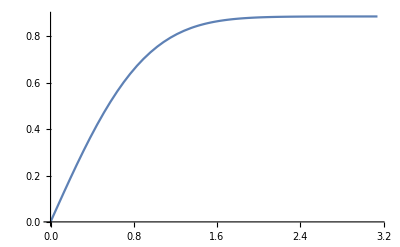
{1.36868,-Graphics-}

```mathematica
AbsoluteTiming[Plot[Integrate[Exp[-y^2],{y,0,x}],{x,0,π}]]
```

Vemos que toma 1.36 segundos en evaluar la integral debido a que la expresion Integrate[Exp[-y^2],{y,0,x}] pasa a Plot
sin evaluar y dentro del algoritmo para ccada valor de x calcula la integral, esta calculando multiples integrales. 
Podemos notar que:

```mathematica
Integrate[Exp[-y^2],{y,0,x}](*Esta integral tiene una funcion interna de mathematica que puede acelerar el proceso*)
```

1/2 √π Erf[x]

```mathematica
AbsoluteTiming[Plot[Evaluate@Integrate[Exp[-y^2],{y,0,x}],{x,0,π}]]
```

{0.0402095,-Graphics-}

Ahora toma 0.04 segundos, dado que utiliza la funcion Erf luego de evaluarse la integral.